```mathematica
(*Fitting a noisy Gaussian with Mathematica*)
(*Brian R. Kent*)
(*Create random Gaussian noise*)
```

```mathematica
noise=0.05*Table[RandomReal[NormalDistribution[0,1]],{201}];
```

```mathematica
(*Plot a Gaussian*)
```

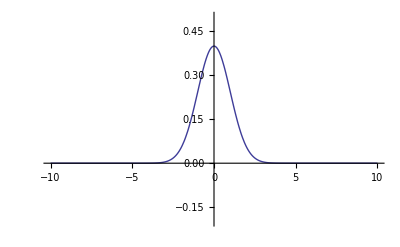

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-10,10}, PlotRange->{{-10,10},{-0.2,0.5}}]
```

```mathematica
(*Create an x array*)
```

```mathematica
x=Table[num,{num,-10,10,0.1}];
```

```mathematica
(*Create a y array*)
```

```mathematica
y=Table[PDF[NormalDistribution[0,1],z],{z,-10,10,0.1}];
```

```mathematica
(*Plot the noisy Gaussian*)
```

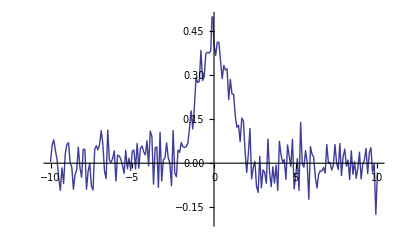

```mathematica
ListLinePlot[Transpose[{x,y+noise}],PlotRange->{{-10,10},{-0.2,0.5}}]
```

```mathematica
(*Create the list of ordered pairs*)
```

```mathematica
data=Transpose[{x,y+noise}];
```

```mathematica
(*Use a Gaussian as a function with free parameters mean and sigma, and variable z*)
```

```mathematica
gaussian=FindFit[data,PDF[NormalDistribution[mean,sigma],z],{mean,sigma},z]
```

{mean→-0.0154826,sigma→0.957597}

```mathematica
(*Evaluate the Gaussian with the determined parameters, and plot the data and the fit*)
```

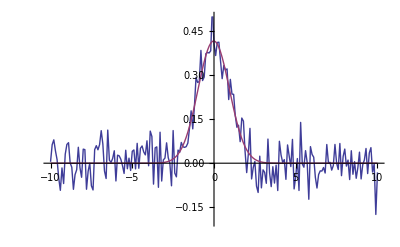

```mathematica
ListLinePlot[{Transpose[{x,y+noise}],Transpose[{x,Table[PDF[NormalDistribution[mean,sigma],z]/.gaussian,{z,-10,10,0.1}]}]},PlotRange->{{-10,10},{-0.2,0.5}}]
```